```mathematica
<<Local`QFTToolKit`
DefineTensorShortcuts[{{Q},1},{{σ},4}]
QCDBaseIndices
DefineDottedIndices
```

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3,4,5,6,7,8}},{color,{1,2,3}},{flavor,{1,2,3,4,5,6}},{family,{1,2,3}}}

```mathematica
DefineTensorShortcuts[{{η,t,δ,ε,λ,D,F,U,"E",H,g,τ,v},1},
{{y,U,u,ψ,V,h},2},
{{σ,λ,T},3}
]
```

Lecture 28 Sept 2011 notes

```mathematica
PR1[""
]
```

```mathematica
PR1["SUSY Breaking.  Ref[Dimopolius-Georgi Theorem:Nucl.Phys. B193 150(1981) about squark mass.]
Theorem: Take 3-2-1 SUSY with super fields {Q, U, D, L, E, Hd[u|d],X} and a SUSY breaking function F_X imply that squarks has mass less than mass of quark which is a disaster since no squarks have been seen.  They assume:
1. SUSY is global
2. 3-2-1 gauge group
3. Dominant contribution are from tree-level diagrams
4. Lagrangian operator dim<=4
5. 4 space-time dimensions
To get around this theorem people have been working mostly on 
1. SUSY is NOT global(called gravity mediation) and T[u,{},{u}]
3. Dominant contribution are NOT from tree-level diagrams (called gauge mediation where SUSY is broken by radiative corrections.) 
The problem stems from terms like ",yd[u].Q.Uu[c].Hd[u]," where with ",Hd[u]," its VEV produces ",Subscript[m, u]->T[u,{},{u}]vd[u] ,
" which comes from the potential, ",V->Abs[xPartialD[W,T[ũ,{c},{}]]]^2->Abs[yd[u].q̃.hd[u]]^2->T[u,{},{u}]^2 vd[u]^2 SuperDagger[q̃].q̃,
" where we can identify as the mass term for ", SuperDagger[q̃].q̃," The consider that the traditional VEV from the superfield ",
H->h+θ.h̃+θ.θ.Fd[H]," comes from the ",h,". However, suppose ",Fd[H]," had a VEV: ",BraKet[Fd[H]] ," then the Lagrangian would contain a mass matrix term: ",
(tmp=xDot[{{SuperDagger[q̃],T[ũ,{c},{}]}},{{yd[u]^2 vd[u]^2,y Fd[H]},{y Fd[H],yd[u]^2 vd[u]^2}},Transpose[{{q̃,SuperDagger[T[ũ,{c},{}]]}}]])//MatrixForms,Yield,
tmp=tmp/.xDot->Dot//Expand," which splits the mass degeneracy between ",{q,q̃},CR[" diagonalize in q,u."]
]
```

SUSY Breaking.  Ref[Dimopolius-Georgi Theorem:Nucl.Phys. B193 150(1981) about squark mass.]
Theorem: Take 3-2-1 SUSY with super fields {Q, U, D, L, E, Hd[u|d],X} and a SUSY breaking function F_X imply that squarks has mass less than mass of quark which is a disaster since no squarks have been seen.  They assume:
1. SUSY is global
2. 3-2-1 gauge group
3. Dominant contribution are from tree-level diagrams
4. Lagrangian operator dim<=4
5. 4 space-time dimensions
To get around this theorem people have been working mostly on 
1. SUSY is NOT global(called gravity mediation) and T[u,{},{u}]
3. Dominant contribution are NOT from tree-level diagrams (called gauge mediation where SUSY is broken by radiative corrections.) 
The problem stems from terms like y_u^u.Q.U_c^c.H_u^u where with H_u^u its VEV produces m_u→u_u^u v_u^u which comes from the potential, V→Abs[UnderBar[∂]_((ũ)_c^c)[W]]^2→Abs[y_u^u.q̃.h_u^u]^2→(q̃)^†.q̃ (u_u^u)^2 (v_u^u)^2 where we can identify as the mass term for (q̃)^†.q̃ The consider that the traditional VEV from the superfield H→h+θ.h̃+θ.θ.F_H^H comes from the h. However, suppose F_H^H had a VEV: ⟨F_H^H⟩ then the Lagrangian would contain a mass matrix term: xDot[((q̃)^† | (ũ)_c^c),((v_u^u)^2 (y_u^u)^2 | y F_H^H
y F_H^H | (v_u^u)^2 (y_u^u)^2),(q̃
((ũ)_c^c)^†)]
→ {{y (q̃)^† ((ũ)_c^c)^† F_H^H+q̃ (q̃)^† (v_u^u)^2 (y_u^u)^2+y q̃ F_H^H (ũ)_c^c+((ũ)_c^c)^† (v_u^u)^2 (y_u^u)^2 (ũ)_c^c}} which splits the mass degeneracy between {q,q̃} diagonalize in q,u.

```mathematica
PR1["Different sectors where there is different physics and all but one are hidden and there is very weak communication between them by messengers (Call mediation.). These can affect interactions.",NL,
Grid[
{{"Visible Sector{Q,U,D,L,F,H}",
"Messenger sector[mediation]",
"Hidden Sector where SUSY is broken by X"}},Frame->All],NL,
Subscript[ℒ, eff]->Subscript[ℒ, stdSUSY]+Subscript[δℒ, SUSY[broken]]  ,NL,
"Would like if ",Subscript[δℒ, SUSY[broken]]->Subscript[m, q̃]^2 SuperDagger[(q̃)].q̃+ Subscript[m, l̃]^2  SuperDagger[(l̃)].l̃+Subscript[m, g̃]^2 SuperDagger[(g̃)].g̃," terms do not destroy SUSY's solution to hierarchy problem for example. The classification is that HARD SUSY breaking does destroy hierarchical problem solution and SOFT SUSY breaking does not.  Example of HARD: "
];
```

Different sectors where there is different physics and all but one are hidden and there is very weak communication between them by messengers (Call mediation.). These can affect interactions.
Visible Sector{Q,U,D,L,F,H} | Messenger sector[mediation] | Hidden Sector where SUSY is broken by X
ℒ_eff→ℒ_stdSUSY+δℒ_SUSY[broken]
Would like if δℒ_SUSY[broken]→(g̃)^†.g̃ m_(g̃)^2+(l̃)^†.l̃ m_(l̃)^2+(q̃)^†.q̃ m_(q̃)^2 terms do not destroy SUSY's solution to hierarchy problem for example. The classification is that HARD SUSY breaking does destroy hierarchical problem solution and SOFT SUSY breaking does not.  Example of HARD:

General graphic definitions for array points and lines.

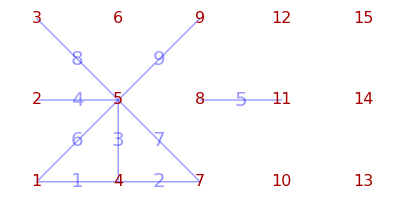

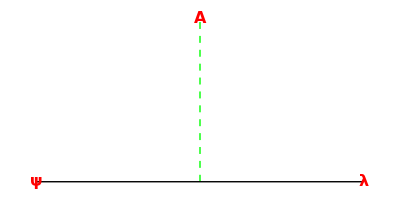
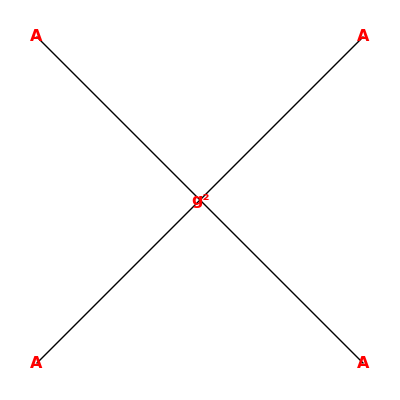
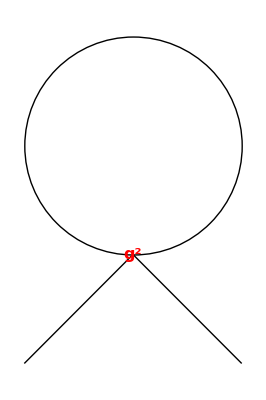
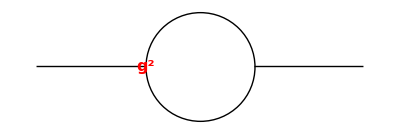
-Graphics- | 
-Graphics- | δ (A^*.A)^2→Λ^2.divergent
-Graphics- | g^2 ∫_k [1/k^2]→Λ^2.divergent
-Graphics- | -g^2 ∫_k [1/k^2]→Λ^2.divergent

```mathematica
{vx,line}=GraphicPointLines[5,3,{{1,4},{4,7},{4,5},{2,5},{8,11},{1,5},{7,5},{3,5},{5,9}}];
Linex[i_]:=Line[line[[i]]]
font:={Red,Bold,16}
PR1[Grid[{
{Graphics[{Thin,Black,
{Dashed,Green,Thick,Linex[3]},
Linex[1],Linex[2],
Text[Style[ψ,font],vx[[1]]],
Text[Style[λ,font],vx[[7]]],
Text[Style[A,font],vx[[5]]]}
]},{
Graphics[{Black,
Linex[6],Linex[7],Linex[8],Linex[9],
Text[Style[A,font],vx[[1]]],Text[Style[A,font],vx[[7]]],Text[Style[A,font],vx[[3]]],Text[Style[A,font],vx[[9]]],Text[Style[g^2,font],vx[[5]]]}
],δ(SuperStar[A].A)^2->(Λ^2)."divergent"},{
Graphics[{Black,
Linex[6],Linex[7],Circle[vx[[6]]],
Text[Style["",font],vx[[1]]],Text[Style["",font],vx[[7]]],Text[Style[g^2,font],vx[[5]]]}
],g^2 IntegralOp[{k},1/k^2]->(Λ^2)."divergent"},{
Graphics[{Black,
Linex[4],Linex[5],Circle[(vx[[5]]+vx[[8]])/2.,.5],
Text[Style["",font],vx[[1]]],Text[Style["",font],vx[[7]]],Text[Style[g^2,font],vx[[5]]]}
],-g^2 IntegralOp[{k},1/k^2]->(Λ^2)."divergent"
}
},Frame->All]
];
```

```mathematica
PR1["How to ensure there is no HARD symmetry breaking.  
Properties of possible SOFT SUSY breaking, Ref: Ghiradello, Grisaru 1981. 
Summary by Murayama:
We have fields:",
Grid[{{"scalar,fermion","gauge"},
{{Ad[i],ψd[i]},{Au[μ],λ}}
},Frame->All],NL,
"Possible soft SUSY breaking terms:",
Grid[{
{(T[m,"dd",{i,j}]^2).SuperStar[Ad[i]].Ad[j],"adds mass to scalars"},
{T[m,"d",{λ}].λ.λ,"adds mass to gauginos"},
{tmp=1/2  T[b,"dd",{i,j}]. T[μ,"dd",{i,j}].Ad[i].Ad[j];tmp+HC[tmp],"bilinear term"},
{tmp=1/2  T[a,"ddd",{i,j,k}]. T[λ,"ddd",{i,j,k}].Ad[i].Ad[j].Ad[k];tmp+HC[tmp],"trilinear term"},
{ψd[i].ψd[j],"for vector-like quantum numbers. Not allowed in MSSM"},
{SuperStar[Ad[i]] Ad[j]Ad[k],"Not allowed in MSSM"},
{ψd[i].λu[a],"cause power divergences"}
},Frame->All]

]
```

How to ensure there is no HARD symmetry breaking.  
Properties of possible SOFT SUSY breaking, Ref: Ghiradello, Grisaru 1981. 
Summary by Murayama:
We have fields:scalar,fermion | gauge
{A_i^i,ψ_i^i} | {A_μ^μ,λ}
Possible soft SUSY breaking terms:(m_ij^ij)^2.(A_i^i)^*.A_j^j | adds mass to scalars
m_λ^λ.λ.λ | adds mass to gauginos
1/2 b_ij^ij.μ_ij^ij.A_i^i.A_j^j+HC[1/2 b_ij^ij.μ_ij^ij.A_i^i.A_j^j] | bilinear term
1/2 a_ijk^ijk.λ_ijk^ijk.A_i^i.A_j^j.A_k^k+HC[1/2 a_ijk^ijk.λ_ijk^ijk.A_i^i.A_j^j.A_k^k] | trilinear term
ψ_i^i.ψ_j^j | for vector-like quantum numbers. Not allowed in MSSM
(A_i^i)^* A_j^j A_k^k | Not allowed in MSSM
ψ_i^i.λ_a^a | cause power divergences

```mathematica
PR1["Example of gravity mediation. Ref[Hall,Lyg? PR D27 p2359(1983)]",
Grid[
{{"graph:",{{q̃,q̃},1/Subscript[M, pl],{⋯},1/Subscript[M, pl],{X,X}},"⟶",IntegralOp[{},_],"⟶",{{Q,Q},Vertex,{X,X}}},
{"Lagrange term:",1/Subscript[M, pl]^2(Q.Q+X.X)[θ θ θ̄ θ̄],"⟶",,"⟶",1/Subscript[M, pl]^2(SuperDagger[q̃].q̃).(SuperDagger[Subscript[F, X]].Subscript[F, X])⇒Subscript[m, q̃]->Subscript[F, X]/Subscript[M, pl]⇒√Subscript[F, X]->√(Subscript[m, q̃] Subscript[M, pl])∼10^11 Gev}
},Frame->All],NL,
"Mass scale of messenger ",Subscript[M, mess]↔Subscript[F, X]," lower if other messengers. The messenger mass scale put constraints on ",Subscript[m, q̃],
" or the gravitino (a candidate for DM)."
];
```

Example of gravity mediation. Ref[Hall,Lyg? PR D27 p2359(1983)]graph: | {{q̃,q̃},1/M_pl,{⋯},1/M_pl,{X,X}} | ⟶ | ∫_ [_] | ⟶ | {{Q,Q},Vertex,{X,X}}
Lagrange term: | ((Q.Q+X.X)[θ^2 (θ̄)^2])/M_pl^2 | ⟶ |  | ⟶ | ((q̃)^†.q̃.(F_X)^†.F_X)/M_pl^2⇒m_(q̃)→F_X/M_pl⇒√F_X→√(m_(q̃) M_pl)∼100000000000 Gev
Mass scale of messenger M_mess↔F_X lower if other messengers. The messenger mass scale put constraints on m_(q̃) or the gravitino (a candidate for DM).

General graphic definitions for array points and lines.

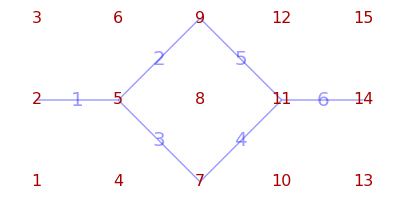

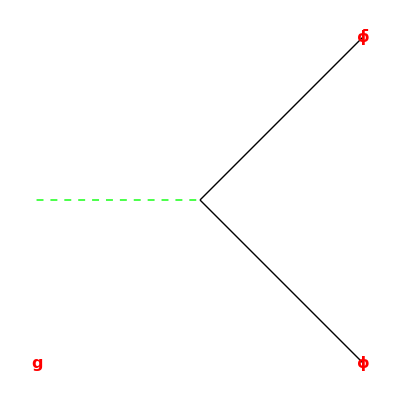
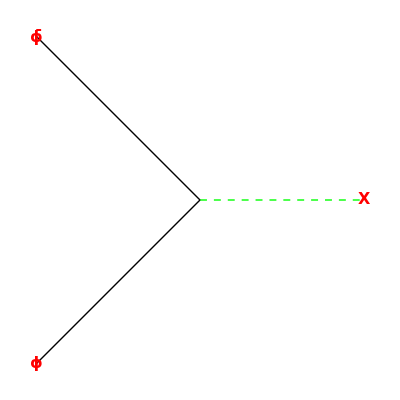
Gauge mediation: ref:Alverez-Gaume,Claudson,Wise NP B207 96(1982) {Standard SUSY} | V[ϕ.ϕ.Vector] | Messenger[ϕ+ϕ̄]
M ϕ ϕ̄ | V[X ϕ^2,adds mass] | ⟨X_F⟩.ϕ_A.ϕ_A
{SUSY breaking w/,ϕ→A+θ.ψ+θ.θ.F}
⟨F_X⟩≠0
 | -Graphics- |  |  | -Graphics-
Two fields carry gauge interation couple to X.  Then ℒ_SUSYbreaking→⟨X_F⟩ (A^2+(A^*)^2)

```mathematica
{vx,line}=GraphicPointLines[5,3,{{2,5},{5,9},{5,7},{7,11},{9,11},{11,14}}];
Linex[i_]:=Line[line[[i]]]
font:={Red,Bold,16}
PR1["Gauge mediation: ref:Alverez-Gaume,Claudson,Wise NP B207 96(1982) ",
Grid[{
{{"Standard SUSY"},V[ϕ. ϕ. "Vector"],Column[{"Messenger[ϕ+ϕ̄]",M ϕ ϕ̄},Center],V[X ϕ ϕ,"adds mass"],
Column[{BraKet[Subscript[X, F]].Subscript[ϕ, A].Subscript[ϕ, A],
{"SUSY breaking w/",ϕ->A+θ.ψ+θ.θ.F},
BraKet[Subscript[F, X]]≠0},Center]},
{,Graphics[{Thin,Black,
{Dashed,Green,Thick,Linex[1]},
Linex[2],
Linex[3],
Text[Style[ϕ,font],vx[[7]]],
Text[Style[ϕ̄,font],vx[[9]]],
Text[Style[g,font],vx[[1]]]
}],,,
Graphics[{Thin,Black,
{Dashed,Green,Thick,Linex[6]},
Linex[4],
Linex[5],
Text[Style[ϕ,font],vx[[7]]],
Text[Style[ϕ̄,font],vx[[9]]],
Text[Style[X,font],vx[[14]]]
}]
}
},Frame->All],NL,
"Two fields carry gauge interation couple to X.  Then ",Subscript[ℒ, SUSYbreaking]->BraKet[Subscript[X, F]](A^2+SuperStar[A]^2)
];
```

General graphic definitions for array points and lines.

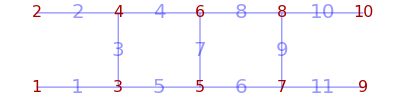

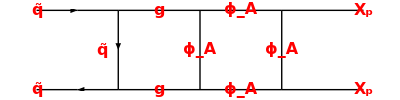

The above X_F cause δM splitting in ψψbar spectrum which would cancel with SUSY self energy diagram below.

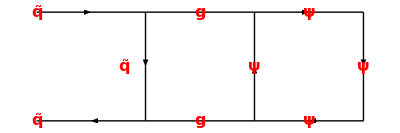

```mathematica
{vx,line}=GraphicPointLines[5,2,{{1,3},{2,4},{3,4},{4,6},{3,5},{5,7},{6,5},{6,8},{8,7},{8,10},{7,9}}];
Linex[i_]:=Line[line[[i]]]
font:={Red,Bold,16}

Graphics[{Thin,Black,
MidArrow[line[[1]]//Reverse],MidArrow[line[[2]]],MidArrow[line[[3]]//Reverse],
Linex[4],Linex[5],Linex[6],Linex[7],Linex[8],Linex[9],Linex[10],Linex[11],
Text[Style[q̃,font],vx[[1]]],
Text[Style[q̃,font],vx[[2]]],
Text[Style[Subscript[X, p],font],vx[[9]]],
Text[Style[Subscript[X, p],font],vx[[10]]],
MidLineTextOffset[q̃,line[[3]],font,{-.2,0}],
MidLineText[g,line[[4]],font],
MidLineText[g,line[[5]],font],
MidLineText[Subscript[ϕ, A],line[[6]],font],
MidLineText[Subscript[ϕ, A],line[[7]],font],
MidLineText[Subscript[ϕ, A],line[[8]],font],
MidLineText[Subscript[ϕ, A],line[[9]],font]
}
]
PR["The above X_F cause δM splitting in ψψbar spectrum which would cancel with SUSY self energy diagram below."
]
Graphics[{Thin,Black,
MidArrow[line[[1]]//Reverse],MidArrow[line[[2]]],MidArrow[line[[3]]//Reverse],
Linex[4],Linex[5],
MidArrow[line[[6]]//Reverse],MidArrow[line[[7]]//Reverse],MidArrow[line[[8]]],MidArrow[line[[9]]],
Text[Style[q̃,font],vx[[1]]],
Text[Style[q̃,font],vx[[2]]],
Text["",vx[[10]]],
MidLineTextOffset[q̃,line[[3]],font,{-.2,0}],
MidLineText[g,line[[4]],font],
MidLineText[g,line[[5]],font],
MidLineText[ψ,line[[6]],font],
MidLineText[ψ,line[[7]],font],
MidLineText[ψ,line[[8]],font],
MidLineText[ψ,line[[9]],font]
}
]
```